# wbBrancSufCond wbBrancNecCond1 wbBrancNecCond2 wbBrancNecCond3

functions that filter the couplings according to the BFB conditions of Branco's model.

## Documentation

### Usage

wbBrancSufCond[list]

Filter the couplings according to the sufficient BFB conditions given in Refs. [1, 2]. The couplings are arranged in the following order: list = {a_1, a_2, a_3, b_1, b_2, b_3, c_1, c_2, c_3, d_1, d_2, d_3}. Return: False | True.

wbBrancNecCond1[list]

Filter the couplings according to the 2HDM necessary BFB conditions (NCL1) given in Ref. [3]. The couplings in list are ordered according to the convention used in wbBrancSufCond. Return: False | True.

wbBrancNecCond2[list]

Filter the couplings according to additional necessary BFB conditions (NCL2-NCL3) given in Ref. [3]. The couplings in list are ordered according to the convention used in wbBrancSufCond. Return: False | True.

wbBrancNecCond3[list, list_1, list_2]

Filter the couplings by imposing additional necessary BFB conditions (NCL4) given in Ref. [3] via a scan over the orbit-space surface using the grids list_(1,2). The couplings in list are ordered according to the convention used in wbBrancSufCond. Return: False | True.

## Examples

To test usage examples make sure the package has been loaded:

```mathematica
wbLoadBinaries=True;(*wpCompTarget="C";*)
NotebookEvaluate[FileNameJoin[{ParentDirectory@NotebookDirectory[EvaluationNotebook[]],"StableWein.nb"}]]
```

### Basic Examples

Generate a set of couplings within the specified range and evaluate the BFB conditions:

```mathematica
couplSet=wbBrancParRndUniNec[]
```

{2.05788,8.31228,2.48585,0.896642,-6.50228,9.55689,-8.06847,7.42616,12.0634,5.08364,-4.21198,4.36192}

```mathematica
wbBrancSufCond[couplSet]
wbBrancNecCond1[couplSet]
wbBrancNecCond2[couplSet]
wbBrancNecCond3[couplSet,wbfaceListBranc,wbθListBranc]
```

False

False

True

True

Fractions of points satisfying the BFB conditions:

```mathematica
data=ParallelTable[wbBrancParRndNec[10],{10^6}];
dataSuf=Pick[data,ParallelMap[wbBrancSufCond,data]];
dataNec1=Pick[data,ParallelMap[wbBrancNecCond1,data]];
dataNec2=Pick[dataNec1,ParallelMap[wbBrancNecCond2,dataNec1]];
dataNec3=Pick[dataNec2,ParallelMap[wbBrancNecCond3[#,wbfaceListBranc,wbθListBranc]&,dataNec2]];
Length/@{dataSuf,dataNec1,dataNec2,dataNec3}
PercentForm/@N[%/Length[data]]
```

{81246,93137,87716,87712}

{8.125%,9.314%,8.772%,8.771%}

All points that satisfy the sufficient BFB conditions also satisfy the necessary 2HDM conditions; however, points that satisfy the necessary 2HDM conditions do not necessarily satisfy the sufficient conditions:

```mathematica
Complement[dataSuf,dataNec1]//Length
Complement[dataNec1,dataSuf]//Length
Pick[dataSuf,ParallelMap[wbBrancNecCond1,dataSuf]]==Pick[dataNec1,ParallelMap[wbBrancSufCond,dataNec1]]
```

0

11891

True

To improve the accuracy of the scan over the orbit-space surface (function wbBrancNecCond3), the scanning grid can be refined by adjusting the parameter values of stepsWein. Note that increasing these values also increases the computation time. For most practical applications, the default settings (stepsBranc = {17, 15}) are sufficient; however, to achieve accuracy close 100% it may be necessary to increase them, for example to stepsWein = {50, 80}.

By default, the global parameters (wbfaceListBranc and  wbθListBranc) specify the following numbers of grid points:

```mathematica
Length/@{wbfaceListBranc,wbθListBranc}
```

{5148,4417}

which enables relatively fast filtering of BFB-allowed points:

```mathematica
data=ParallelTable[wbBrancParRndNec[10],{10^3}];
Length[Pick[data,ParallelMap[wbBrancNecCond3[#,wbfaceListBranc,wbθListBranc]&,data]]]//AbsoluteTiming
```

{0.164246,353}

Using wbBrancGridGen, we increase the number of grid points:

```mathematica
stepsBranc={33,30};
{wbfaceListBranc,wbθListBranc}=wbBrancGridGen[stepsBranc];
```

Number of points in Branco's grids: {36109, 32217}

which allows BFB-allowed points to be filtered more accurately, at the cost of increased computational time:

```mathematica
Length[Pick[data,ParallelMap[wbBrancNecCond3[#,wbfaceListBranc,wbθListBranc]&,data]]]//AbsoluteTiming
```

{1.29028,350}

Note that, in combination with wbBrancSufCond and wbBrancNecCond2, the function wbBrancNecCond3 yields highly accurate results even with the default grids, as can be seen in wbBrancUniBFBcheck.

### Scope

Couplings are generated in the range ∣coupling∣ ≤ 10 and are then filtered to retain only those that satisfy the relevant BFB conditions.

```mathematica
dataNec1=ParallelTable[testT=False; While[testT==False,paramT=wbBrancParRndNec[10]; testT=wbBrancNecCond1[paramT]]; paramT,{10^6}];
dataNec2=Pick[dataNec1,ParallelMap[wbBrancNecCond2,dataNec1]];
dataSuf=Pick[dataNec1,ParallelMap[wbBrancSufCond,dataNec1]];
Length/@{dataNec1,dataNec2,dataSuf}
PercentForm/@N[%/Length[dataNec1]]
```

{1000000,942862,873124}

{100%,94.29%,87.31%}

```mathematica
parNames={"a_1","a_2","a_3","b_1","b_2","b_3","c_1","c_2","c_3","d_1","d_2","d_3"};
table1=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataNec1),TableHeadings->{parNames,{"Min","Max"}}]; 
table2=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataNec2),TableHeadings->{parNames,{"Min","Max"}}]; 
table3=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataSuf),TableHeadings->{parNames,{"Min","Max"}}];
Grid[#,Spacings->{0, 1}]&/@(Partition[#,1]&/@Transpose[{{"wbBrancNecCond1","wbBrancNecCond2","wbBrancSufCond"},{table1,table2,table3}}]);
Grid[{%},Spacings->{4, 0}]
```

wbBrancNecCond1
 | Min | Max
a_1 | 0. | 10.
a_2 | 0. | 10.
a_3 | 0. | 10.
b_1 | -9.85 | 10.
b_2 | -9.89 | 10.
b_3 | -9.82 | 10.
c_1 | -10. | 10.
c_2 | -10. | 10.
c_3 | -10. | 10.
d_1 | -10. | 10.
d_2 | -10. | 10.
d_3 | -10. | 10. | wbBrancNecCond2
 | Min | Max
a_1 | 0. | 10.
a_2 | 0. | 10.
a_3 | 0. | 10.
b_1 | -9.85 | 10.
b_2 | -9.74 | 10.
b_3 | -9.82 | 10.
c_1 | -10. | 10.
c_2 | -10. | 10.
c_3 | -10. | 10.
d_1 | -10. | 10.
d_2 | -10. | 10.
d_3 | -10. | 10. | wbBrancSufCond
 | Min | Max
a_1 | 0. | 10.
a_2 | 0. | 10.
a_3 | 0. | 10.
b_1 | -9.73 | 10.
b_2 | -9.73 | 10.
b_3 | -9.81 | 10.
c_1 | -10. | 10.
c_2 | -10. | 10.
c_3 | -10. | 10.
d_1 | -10. | 10.
d_2 | -10. | 10.
d_3 | -10. | 10.

Distribution of the couplings filtered with function wbBrancNecCond1 (green contour), function  wbBrancNecCond2 (blue dashed contour), and function  wbBrancSufCond (red dashed contour):

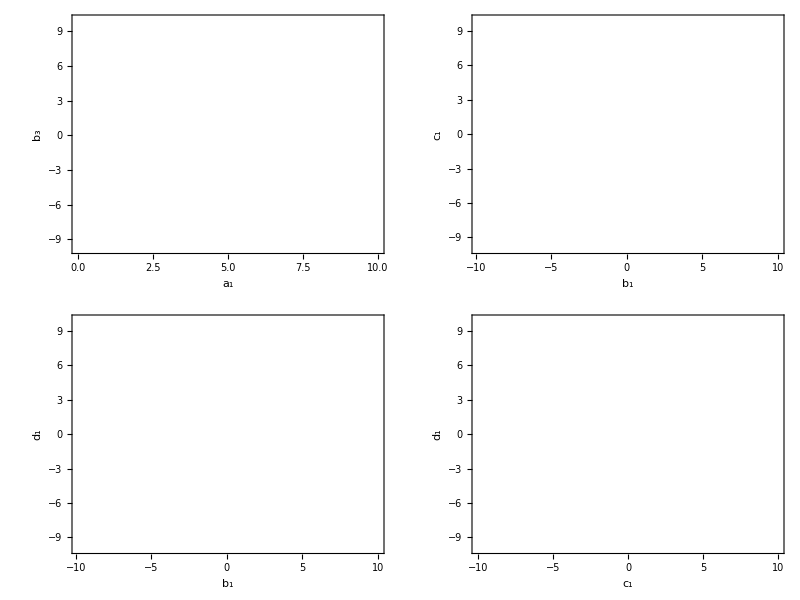

```mathematica
Table[Show[{ConvexHullMesh[dataNec1[[;;,xx]],MeshCellStyle->{1->{Darker[Green,0.2]},2->Opacity[0,Green]}],ConvexHullMesh[dataNec2[[;;,xx]],MeshCellStyle->{1->{Blue,Dashed},2->Opacity[0,Blue]}],ConvexHullMesh[dataSuf[[;;,xx]],MeshCellStyle->{1->{Red,Dashed},2->Opacity[0,Red]}]},PlotRange->Automatic,Frame->True,AspectRatio->1,FrameStyle->Black,ImageSize->250,FrameLabel->{Style[parNames⟦xx[[1]]⟧,16,Black],Style[parNames⟦xx[[2]]⟧,16,Black]}],{xx,{{1,6},{4,7},{4,10},{7,10}}}];
Grid[Partition[%,2]]
```

Couplings are generated to satisfy the UNI and NCL1 conditions, and are then filtered to retain only those that also satisfy the NCL2-NCL3 or sufficient BFB conditions:

```mathematica
dataUniNec1=ParallelTable[testT=False; While[testT==False,paramT=wbBrancParRndUniNec[]; testT=wbBrancUNINec1Cond[paramT,8.*Pi]]; paramT,{10^6}];
dataUniNec2=Pick[dataUniNec1,ParallelMap[wbBrancNecCond2,dataUniNec1]];
dataUniSuf=Pick[dataUniNec1,ParallelMap[wbBrancSufCond,dataUniNec1]];
Length/@{dataUniNec1,dataUniNec2,dataUniSuf}
PercentForm/@N[%/Length[dataUniNec1]]
```

{1000000,750377,601547}

{100%,75.04%,60.15%}

```mathematica
parNames={"a_1","a_2","a_3","b_1","b_2","b_3","c_1","c_2","c_3","d_1","d_2","d_3","ϵ"};
table1=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataUniNec1),TableHeadings->{parNames,{"Min","Max"}}]; 
table2=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataUniNec2),TableHeadings->{parNames,{"Min","Max"}}]; 
table3=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataUniSuf),TableHeadings->{parNames,{"Min","Max"}}];
Grid[#,Spacings->{0, 1}]&/@(Partition[#,1]&/@Transpose[{{"wbBrancNecCond1","wbBrancNecCond2","wbBrancSufCond"},{table1,table2,table3}}]);
Grid[{%},Spacings->{4, 0}]
```

wbBrancNecCond1
 | Min | Max
a_1 | 0. | 8.38
a_2 | 0. | 8.37
a_3 | 0. | 8.38
b_1 | -7.78 | 15.7
b_2 | -7.58 | 15.55
b_3 | -7.5 | 15.43
c_1 | -16.09 | 15.77
c_2 | -15.7 | 15.88
c_3 | -15.82 | 15.65
d_1 | -8.24 | 8.23
d_2 | -8.15 | 8.1
d_3 | -8.13 | 8.16 | wbBrancNecCond2
 | Min | Max
a_1 | 0. | 8.38
a_2 | 0. | 8.37
a_3 | 0. | 8.38
b_1 | -7.38 | 15.7
b_2 | -7.45 | 15.55
b_3 | -7.38 | 15.43
c_1 | -15.58 | 15.22
c_2 | -15.48 | 15.88
c_3 | -15.82 | 15.42
d_1 | -8.03 | 7.98
d_2 | -8. | 8.
d_3 | -7.99 | 8.01 | wbBrancSufCond
 | Min | Max
a_1 | 0. | 8.38
a_2 | 0. | 8.37
a_3 | 0. | 8.38
b_1 | -7.22 | 15.7
b_2 | -7.45 | 15.55
b_3 | -7.24 | 15.43
c_1 | -14.93 | 15.22
c_2 | -15.48 | 15.88
c_3 | -14.91 | 15.42
d_1 | -7.8 | 7.72
d_2 | -7.75 | 7.92
d_3 | -7.76 | 7.91

Distribution of the couplings satisfying UNI conditions and filtered with function wbBrancNecCond1 (green contour), function  wbBrancNecCond2 (blue dashed contour), and function  wbBrancSufCond (red dashed contour):

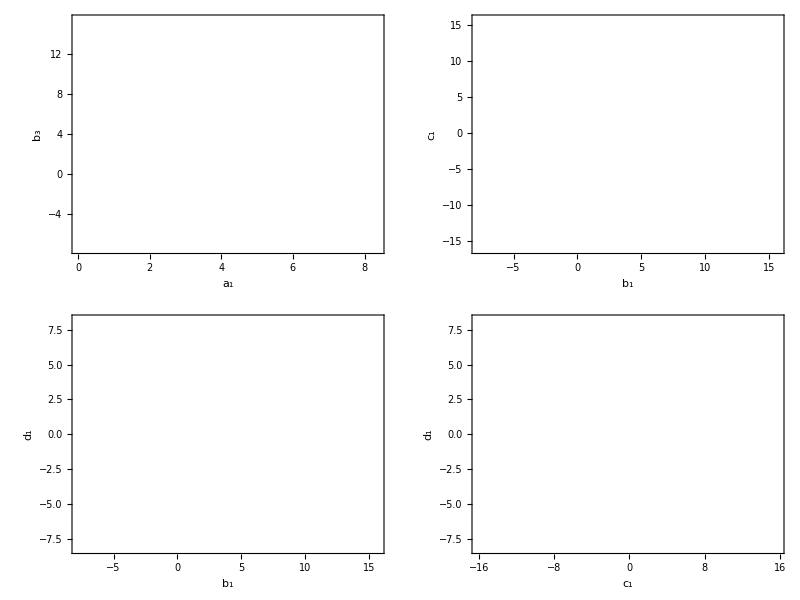

```mathematica
Table[Show[{ConvexHullMesh[dataUniNec1[[;;,xx]],MeshCellStyle->{1->{Darker[Green,0.2]},2->Opacity[0,Green]}],ConvexHullMesh[dataUniNec2[[;;,xx]],MeshCellStyle->{1->{Blue,Dashed},2->Opacity[0,Blue]}],ConvexHullMesh[dataUniSuf[[;;,xx]],MeshCellStyle->{1->{Red,Dashed},2->Opacity[0,Red]}]},PlotRange->Automatic,Frame->True,AspectRatio->1,FrameStyle->Black,ImageSize->250,FrameLabel->{Style[parNames⟦xx[[1]]⟧,16,Black],Style[parNames⟦xx[[2]]⟧,16,Black]}],{xx,{{1,6},{4,7},{4,10},{7,10}}}];
Grid[Partition[%,2]]
```

### Options

## Source & Additional Information

### Related Symbols

wbBrancParRnd ▪ wbBrancParRndNec ▪ wbBrancParRndUni ▪ wbBrancParRndUniNec ▪ wbBrancUNICond ▪ wbBrancUNINec1Cond ▪ wbBrancUniBFBcheck

### References

[1] R. Boto, J.C. Romao and J.P. Silva, Bounded from below conditions on a class of symmetry constrained 3HDM, Phys. Rev. D 106 (2022) no.11, 115010 https://doi.org/10.1103/PhysRevD.106.115010 [arXiv:2208.01068 [hep-ph]].

[2] B. Grzadkowski, O.M. Ogreid and P. Osland, Natural Multi-Higgs Model with Dark Matter and CP Violation, Phys. Rev. D 80 (2009), 055013 https://doi.org/10.1103/PhysRevD.80.055013 [arXiv:0904.2173 [hep-ph]].

[3] D. Jurčiukonis, L. Lavoura and A. Milagre, Assessing boundedness from below in the Z_2 x Z_2-symmetric three-Higgs-doublet model: algorithm and machine learning, arXiv:2603.23590 [hep-ph].